# Lista 3

## Exercise 1

We want to proof a theorem for a general 3x3 matrix:

```mathematica
ClearAll[A,a,b,c,d,e,f,g,h,i]
A={{a,b,c},{d,e,f},{g,h,i}}
FullSimplify[MatrixPower[A,3]-Tr[A]MatrixPower[A,2]+1/2((Tr[A])^2-Tr[MatrixPower[A,2]])A-Det[A]IdentityMatrix[3]]==0
```

{{a,b,c},{d,e,f},{g,h,i}}

{{0,0,0},{0,0,0},{0,0,0}}==0

## Exercise 2

We want to proof a theorem for two general 2x2 matrices:

```mathematica
ClearAll[A,B,a,b,c,d,e,f,g,h]
A={{a,b},{c,d}}
B={{e,f},{g,h}}
FullSimplify[(Tr[A.B]-Tr[A]Tr[B])IdentityMatrix[2]+Tr[B]A+Tr[A]B-A.B-B.A]//MatrixForm
```

{{a,b},{c,d}}

{{e,f},{g,h}}

(0 | 0
0 | 0)

## Exercise 3

We want to compute rankt of the matrices and find their biggest minor:

```mathematica
M1={{3,1,1,2,-1},{0,2,-1,1,2},{4,3,2,-1,1},{12,9,8,-7,3},{-12,-5,-8,5,1}}
MatrixRank[M1]
Minors[M1,MatrixRank[M1]]
```

{{3,1,1,2,-1},{0,2,-1,1,2},{4,3,2,-1,1},{12,9,8,-7,3},{-12,-5,-8,5,1}}

4

{{18,-8,16,14,0},{0,0,0,0,0},{54,-24,48,42,0},{36,-16,32,28,0},{0,0,0,0,0}}

```mathematica
M2={{1,1,1,1},{4,3,2,1},{1,4,1,1},{5,1,1,1},{1,1,3,1},{1,1,1,2}}
MatrixRank[M2]
Minors[M1,MatrixRank[M2]]
```

{{1,1,1,1},{4,3,2,1},{1,4,1,1},{5,1,1,1},{1,1,3,1},{1,1,1,2}}

4

{{18,-8,16,14,0},{0,0,0,0,0},{54,-24,48,42,0},{36,-16,32,28,0},{0,0,0,0,0}}

## Exercise 4

We present a table witch names of European Capital Cities and their temperature:

```mathematica
TmpCapt=CountryData["Europe","CapitalCity"];
TC=Table[TmpCapt[[i]][[2]][[1]],{i,1,Length[TmpCapt]}];
tc[u_]:=WeatherData[u,"Temperature"];
FinalCT=Map[tc,TC];
FinalData=Transpose[{TC,FinalCT}];
TableForm[FinalData,TableHeadings->{Table[" ",{k,1,Length[FinalData]}],{" "," "}}]
```

|   |  
  | Tirana | 6.
  | AndorraLaVella | 2.2
  | Vienna | 8.5
  | Minsk | 1.8
  | Brussels | 11.5
  | Sarajevo | 2.
  | Sofia | 7.
  | Zagreb | 9.
  | Nicosia | 19.
  | Prague | 6.4
  | Copenhagen | 4.
  | Tallinn | 4.
  | Torshavn | 4.8
  | Helsinki | 2.
  | Paris | 11.
  | Berlin | 5.2
  | Gibraltar | 15.4
  | Athens | 16.4
  | SaintPeterPort | 12.
  | Budapest | 7.3
  | Reykjavik | -1.9
  | Dublin | 11.
  | Douglas | 12.
  | Rome | 15.
  | SaintHelier | 12.
  | Pristina | 7.7
  | Riga | 3.
  | Vaduz | 7.6
  | Vilnius | 2.
  | Luxemburg | 9.
  | Skopje | 2.
  | Valletta | 15.
  | Chisinau | 5.
  | MonacoVille | 9.
  | Podgorica | 6.1
  | Amsterdam | 13.
  | Oslo | 2.7
  | Warsaw | 3.
  | Lisbon | 14.8
  | Bucharest | 7.
  | SanMarino | 20.
  | Belgrade | 11.3
  | Bratislava | 7.
  | Ljubljana | 8.5
  | Madrid | 7.
  | Longyearbyen | 2.2
  | Stockholm | 1.
  | Bern | 3.3
  | Kiev | 1.
  | London | 14.
  | VaticanCity | 15.

## Exercise 5

We want to compute rankt of the matrix:

```mathematica
la={{7-λ,-12,6},{10,-λ-19,10},{12,-24,13-λ}}
Det[la]
MatrixRank[la]
```

{{7-λ,-12,6},{10,-19-λ,10},{12,-24,13-λ}}

-1+λ+λ^2-λ^3

3

## Exercise 6

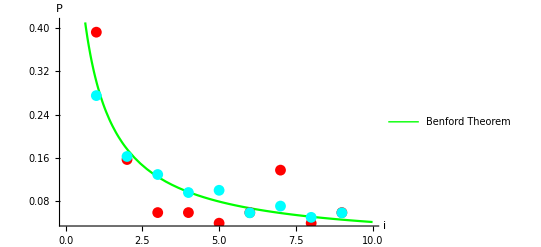

```mathematica
TDigits=Map[RealDigits,FinalCT[[All,1]]];
Dig=Table[TDigits[[i]][[1]][[1]],{i,1,Length[FinalCT]}];
EqN[n_,x_]:=If[n==x,1,0]
Tempd=Table[0,{i,1,9}];
For[k=1,k≤9,k++,For[i=1,i≤Length[Dig],i++,If[Dig[[i]]==k,Tempd[[k]]++,]]];
Tempd=Tempd/Length[Dig]//N;
Temp=ListPlot[Tempd,PlotStyle->Red];

Nms=Table[CountryData[All][[i]][[2]],{i,1,Length[CountryData[All]]}];
GivePop[name_]:=CountryData[name,"Population"]
Pops=Map[GivePop,Nms][[All,1]];
PopDigits=Map[IntegerDigits,Pops][[All]];
DigP=Table[PopDigits[[i]][[1]],{i,1,Length[Pops]}];
Popd=Table[0,{i,1,9}];
For[k=1,k≤9,k++,For[i=1,i≤Length[DigP],i++,If[DigP[[i]]==k,Popd[[k]]++,]]];
Popd=Popd/Length[Pops]//N;
PopPlot=ListPlot[Popd,PlotStyle->Cyan];

Theorem=Plot[Log10[1+1/x],{x,0,10},PlotStyle->Green,AxesLabel->{"i","P"},PlotLegends->{LineLegend[{Green},{"Benford Theorem"}],PointLegend[{Red,Cyan},{"Temperatures","Population"}]}];
Show[Theorem,Temp,PopPlot]
```

## Exercise 7

```mathematica
Map[Characters,Nms]
```

{{A,f,g,h,a,n,i,s,t,a,n},{A,l,b,a,n,i,a},{A,l,g,e,r,i,a},{A,m,e,r,i,c,a,n,S,a,m,o,a},{A,n,d,o,r,r,a},{A,n,g,o,l,a},{A,n,g,u,i,l,l,a},{A,n,t,i,g,u,a,B,a,r,b,u,d,a},{A,r,g,e,n,t,i,n,a},{A,r,m,e,n,i,a},{A,r,u,b,a},{A,u,s,t,r,a,l,i,a},{A,u,s,t,r,i,a},{A,z,e,r,b,a,i,j,a,n},{B,a,h,a,m,a,s},{B,a,h,r,a,i,n},{B,a,n,g,l,a,d,e,s,h},{B,a,r,b,a,d,o,s},{B,e,l,a,r,u,s},{B,e,l,g,i,u,m},{B,e,l,i,z,e},{B,e,n,i,n},{B,e,r,m,u,d,a},{B,h,u,t,a,n},{B,o,l,i,v,i,a},{B,o,s,n,i,a,H,e,r,z,e,g,o,v,i,n,a},{B,o,t,s,w,a,n,a},{B,r,a,z,i,l},{B,r,i,t,i,s,h,V,i,r,g,i,n,I,s,l,a,n,d,s},{B,r,u,n,e,i},{B,u,l,g,a,r,i,a},{B,u,r,k,i,n,a,F,a,s,o},{B,u,r,u,n,d,i},{C,a,m,b,o,d,i,a},{C,a,m,e,r,o,o,n},{C,a,n,a,d,a},{C,a,p,e,V,e,r,d,e},{C,a,y,m,a,n,I,s,l,a,n,d,s},{C,e,n,t,r,a,l,A,f,r,i,c,a,n,R,e,p,u,b,l,i,c},{C,h,a,d},{C,h,i,l,e},{C,h,i,n,a},{C,h,r,i,s,t,m,a,s,I,s,l,a,n,d},{C,o,c,o,s,K,e,e,l,i,n,g,I,s,l,a,n,d,s},{C,o,l,o,m,b,i,a},{C,o,m,o,r,o,s},{C,o,o,k,I,s,l,a,n,d,s},{C,o,s,t,a,R,i,c,a},{C,r,o,a,t,i,a},{C,u,b,a},{C,u,r,a,c,a,o},{C,y,p,r,u,s},{C,z,e,c,h,R,e,p,u,b,l,i,c},{D,e,m,o,c,r,a,t,i,c,R,e,p,u,b,l,i,c,C,o,n,g,o},{D,e,n,m,a,r,k},{D,j,i,b,o,u,t,i},{D,o,m,i,n,i,c,a},{D,o,m,i,n,i,c,a,n,R,e,p,u,b,l,i,c},{E,a,s,t,T,i,m,o,r},{E,c,u,a,d,o,r},{E,g,y,p,t},{E,l,S,a,l,v,a,d,o,r},{E,q,u,a,t,o,r,i,a,l,G,u,i,n,e,a},{E,r,i,t,r,e,a},{E,s,t,o,n,i,a},{E,t,h,i,o,p,i,a},{F,a,l,k,l,a,n,d,I,s,l,a,n,d,s},{F,a,r,o,e,I,s,l,a,n,d,s},{F,i,j,i},{F,i,n,l,a,n,d},{F,r,a,n,c,e},{F,r,e,n,c,h,G,u,i,a,n,a},{F,r,e,n,c,h,P,o,l,y,n,e,s,i,a},{G,a,b,o,n},{G,a,m,b,i,a},{G,a,z,a,S,t,r,i,p},{G,e,o,r,g,i,a},{G,e,r,m,a,n,y},{G,h,a,n,a},{G,i,b,r,a,l,t,a,r},{G,r,e,e,c,e},{G,r,e,e,n,l,a,n,d},{G,r,e,n,a,d,a},{G,u,a,d,e,l,o,u,p,e},{G,u,a,m},{G,u,a,t,e,m,a,l,a},{G,u,e,r,n,s,e,y},{G,u,i,n,e,a},{G,u,i,n,e,a,B,i,s,s,a,u},{G,u,y,a,n,a},{H,a,i,t,i},{H,o,n,d,u,r,a,s},{H,o,n,g,K,o,n,g},{H,u,n,g,a,r,y},{I,c,e,l,a,n,d},{I,n,d,i,a},{I,n,d,o,n,e,s,i,a},{I,r,a,n},{I,r,a,q},{I,r,e,l,a,n,d},{I,s,l,e,O,f,M,a,n},{I,s,r,a,e,l},{I,t,a,l,y},{I,v,o,r,y,C,o,a,s,t},{J,a,m,a,i,c,a},{J,a,p,a,n},{J,e,r,s,e,y},{J,o,r,d,a,n},{K,a,z,a,k,h,s,t,a,n},{K,e,n,y,a},{K,i,r,i,b,a,t,i},{K,o,s,o,v,o},{K,u,w,a,i,t},{K,y,r,g,y,z,s,t,a,n},{L,a,o,s},{L,a,t,v,i,a},{L,e,b,a,n,o,n},{L,e,s,o,t,h,o},{L,i,b,e,r,i,a},{L,i,b,y,a},{L,i,e,c,h,t,e,n,s,t,e,i,n},{L,i,t,h,u,a,n,i,a},{L,u,x,e,m,b,o,u,r,g},{M,a,c,a,u},{M,a,c,e,d,o,n,i,a},{M,a,d,a,g,a,s,c,a,r},{M,a,l,a,w,i},{M,a,l,a,y,s,i,a},{M,a,l,d,i,v,e,s},{M,a,l,i},{M,a,l,t,a},{M,a,r,s,h,a,l,l,I,s,l,a,n,d,s},{M,a,r,t,i,n,i,q,u,e},{M,a,u,r,i,t,a,n,i,a},{M,a,u,r,i,t,i,u,s},{M,a,y,o,t,t,e},{M,e,x,i,c,o},{M,i,c,r,o,n,e,s,i,a},{M,o,l,d,o,v,a},{M,o,n,a,c,o},{M,o,n,g,o,l,i,a},{M,o,n,t,e,n,e,g,r,o},{M,o,n,t,s,e,r,r,a,t},{M,o,r,o,c,c,o},{M,o,z,a,m,b,i,q,u,e},{M,y,a,n,m,a,r},{N,a,m,i,b,i,a},{N,a,u,r,u},{N,e,p,a,l},{N,e,t,h,e,r,l,a,n,d,s},{N,e,w,C,a,l,e,d,o,n,i,a},{N,e,w,Z,e,a,l,a,n,d},{N,i,c,a,r,a,g,u,a},{N,i,g,e,r},{N,i,g,e,r,i,a},{N,i,u,e},{N,o,r,f,o,l,k,I,s,l,a,n,d},{N,o,r,t,h,e,r,n,M,a,r,i,a,n,a,I,s,l,a,n,d,s},{N,o,r,t,h,K,o,r,e,a},{N,o,r,w,a,y},{O,m,a,n},{P,a,k,i,s,t,a,n},{P,a,l,a,u},{P,a,n,a,m,a},{P,a,p,u,a,N,e,w,G,u,i,n,e,a},{P,a,r,a,g,u,a,y},{P,e,r,u},{P,h,i,l,i,p,p,i,n,e,s},{P,i,t,c,a,i,r,n,I,s,l,a,n,d,s},{P,o,l,a,n,d},{P,o,r,t,u,g,a,l},{P,u,e,r,t,o,R,i,c,o},{Q,a,t,a,r},{R,e,p,u,b,l,i,c,C,o,n,g,o},{R,e,u,n,i,o,n},{R,o,m,a,n,i,a},{R,u,s,s,i,a},{R,w,a,n,d,a},{S,a,i,n,t,H,e,l,e,n,a},{S,a,i,n,t,K,i,t,t,s,N,e,v,i,s},{S,a,i,n,t,L,u,c,i,a},{S,a,i,n,t,P,i,e,r,r,e,M,i,q,u,e,l,o,n},{S,a,i,n,t,V,i,n,c,e,n,t,G,r,e,n,a,d,i,n,e,s},{S,a,m,o,a},{S,a,n,M,a,r,i,n,o},{S,a,o,T,o,m,e,P,r,i,n,c,i,p,e},{S,a,u,d,i,A,r,a,b,i,a},{S,e,n,e,g,a,l},{S,e,r,b,i,a},{S,e,y,c,h,e,l,l,e,s},{S,i,e,r,r,a,L,e,o,n,e},{S,i,n,g,a,p,o,r,e},{S,i,n,t,M,a,a,r,t,e,n},{S,l,o,v,a,k,i,a},{S,l,o,v,e,n,i,a},{S,o,l,o,m,o,n,I,s,l,a,n,d,s},{S,o,m,a,l,i,a},{S,o,u,t,h,A,f,r,i,c,a},{S,o,u,t,h,K,o,r,e,a},{S,o,u,t,h,S,u,d,a,n},{S,p,a,i,n},{S,r,i,L,a,n,k,a},{S,u,d,a,n},{S,u,r,i,n,a,m,e},{S,v,a,l,b,a,r,d},{S,w,a,z,i,l,a,n,d},{S,w,e,d,e,n},{S,w,i,t,z,e,r,l,a,n,d},{S,y,r,i,a},{T,a,i,w,a,n},{T,a,j,i,k,i,s,t,a,n},{T,a,n,z,a,n,i,a},{T,h,a,i,l,a,n,d},{T,o,g,o},{T,o,k,e,l,a,u},{T,o,n,g,a},{T,r,i,n,i,d,a,d,T,o,b,a,g,o},{T,u,n,i,s,i,a},{T,u,r,k,e,y},{T,u,r,k,m,e,n,i,s,t,a,n},{T,u,r,k,s,C,a,i,c,o,s,I,s,l,a,n,d,s},{T,u,v,a,l,u},{U,g,a,n,d,a},{U,k,r,a,i,n,e},{U,n,i,t,e,d,A,r,a,b,E,m,i,r,a,t,e,s},{U,n,i,t,e,d,K,i,n,g,d,o,m},{U,n,i,t,e,d,S,t,a,t,e,s},{U,n,i,t,e,d,S,t,a,t,e,s,V,i,r,g,i,n,I,s,l,a,n,d,s},{U,r,u,g,u,a,y},{U,z,b,e,k,i,s,t,a,n},{V,a,n,u,a,t,u},{V,a,t,i,c,a,n,C,i,t,y},{V,e,n,e,z,u,e,l,a},{V,i,e,t,n,a,m},{W,a,l,l,i,s,F,u,t,u,n,a},{W,e,s,t,B,a,n,k},{W,e,s,t,e,r,n,S,a,h,a,r,a},{Y,e,m,e,n},{Z,a,m,b,i,a},{Z,i,m,b,a,b,w,e}}

## Exercise 8

```mathematica
Neighbors=Table[CountryData["Poland","BorderingCountries"][[i]][[2]],{i,1,Length[CountryData["Poland","BorderingCountries"]]}]
NeighborsCapitols=Table[CountryData[Neighbors[[i]],"CapitalCity"][[2]][[1]],{i,1,Length[CountryData["Poland","BorderingCountries"]]}]
NTemps=Map[tc,NeighborsCapitols]
```

{Belarus,CzechRepublic,Germany,Lithuania,Russia,Slovakia,Ukraine}

{Minsk,Prague,Berlin,Vilnius,Moscow,Bratislava,Kiev}

{1.8,6.4,5.4,2.,1.1,6.2,1.}

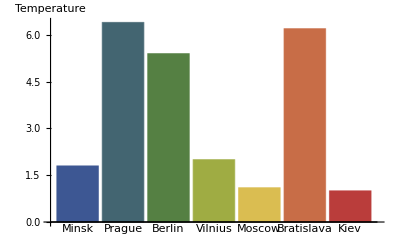

```mathematica
BarChart[NTemps,ChartLabels->NeighborsCapitols,AxesLabel->{None,"Temperature"},ChartStyle->"DarkRainbow"]
```

## Exercise 9